### Vesicle scaffold vs MAPKpp (pnas model) input dose vs [membrane scaffold, vesicle scaffold, MAPKpp] Blue: Native scaffold Purpule: overexpressed scaffold

#### Native scaffold stays on the left side of the bell curve for all input dose. Overexpressed scaffold quickly crosses over the bell curve and stays on the failing side

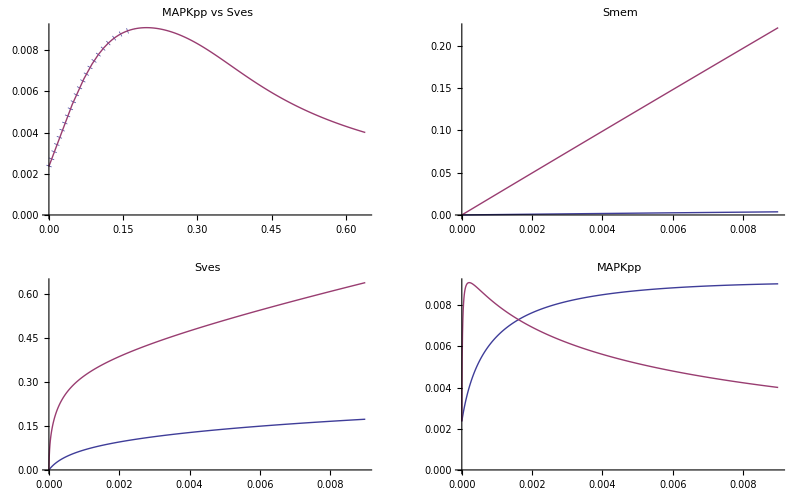

### Smem →^p3Sves The rate membrane scaffold is transported to the vesicies is inhibited by the amount of membrane scaffold

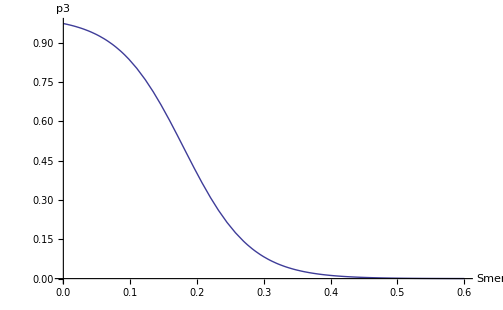

```mathematica
Plot[p3b/(1+Exp[p3c(s-p3a)])/.{p3a->0.18,p3b->1,p3c->20,p3d->.05}//Evaluate,{s,0,0.6},PlotRange->All,AxesLabel->{"Smem","p3"}]
```

### Adding the above inhibition effect to the model creates the inverted bell curve for MAPKpp vs dose At low dosage, scaffold membrane to vesicle transport is unimpeded and thus decreases MAPKpp activity. At high dosage, transport is inhibited, reducing scaffold vescile concentrations, increasing MAPKpp activity.

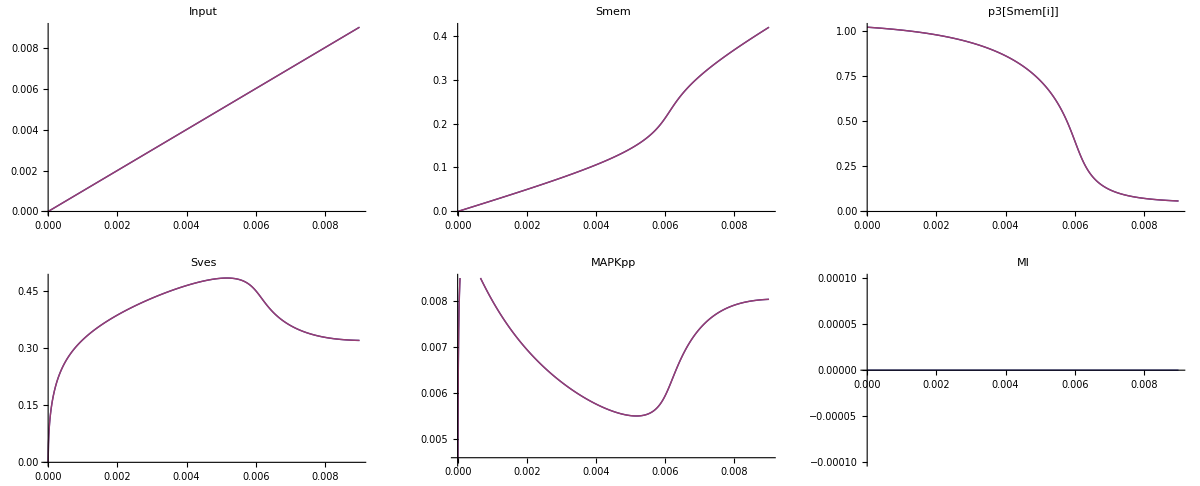

#### The migration index is the derivative of the MAPKpp vs dose curve (MI = MAPKpp_front-MAPKpp_back)

#### Intuitively, the inverted bell curve should mean that for lose dose we get chemorepulsion (negative MI) and at high dose we get chemoattraction (postive MI). However, this is not what happens:

### When the front of the cell has higher input, membrane scaffold to vesicle transport is reduced leading to higher MAPKpp activity. This results in chemoattraction at low dose and chemorepulsion at high dosge, despite the inverted bell curve. It’s like the bell curve shifted the wrong way. Purple: front of cell Blue: back of cell